```mathematica
V[m_,γ_, Δ_] = -Integrate[-r/2*(8*γ*(1-6*γ)*(r^2-1)+4*γ^2*Δ), {r,0,m}]
```

-2 m^2 γ+m^4 γ+12 m^2 γ^2-6 m^4 γ^2+m^2 γ^2 Δ

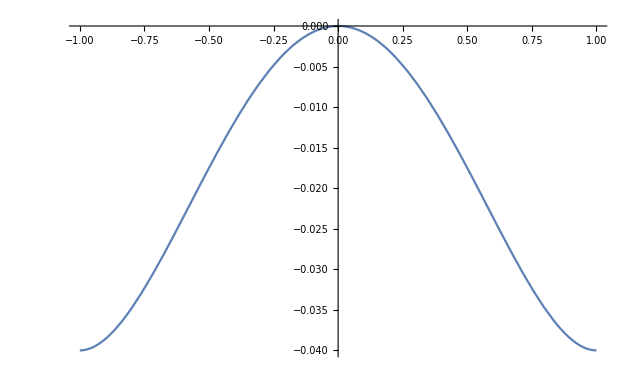

```mathematica
Plot[V[m,0.1,0.001],{m,-1,1}]
```

```mathematica
q = 368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2
```

368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2

```mathematica
Clear[Z]
Z [γ_,Δ_]= Integrate[Exp[-V[m,γ, Δ]/q],{m,-1,1}]
```

∫_-1^1 ⅇ^((2 m^2 γ-m^4 γ-12 m^2 γ^2+6 m^4 γ^2-m^2 γ^2 Δ)/(368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2))ⅆm

```mathematica
W[m_,γ_,Δ_] = 1/Z [γ,Δ]*Exp[-V[m,γ, Δ]/q];
```

```mathematica
Peq[γ_,Δ_,r_] = Integrate[W[m,γ,Δ],{m,-r,r}]
```

∫_-r^r (ⅇ^((2 m^2 γ-m^4 γ-12 m^2 γ^2+6 m^4 γ^2-m^2 γ^2 Δ)/(368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2)))/(∫_-1^1 ⅇ^((2 m^2 γ-m^4 γ-12 m^2 γ^2+6 m^4 γ^2-m^2 γ^2 Δ)/(368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2))ⅆm)ⅆm

```mathematica
τ[γ_,Δ_,r_] = 1/(1-Peq[γ,Δ,r])Integrate[P[t]-Peq,{t,0,+Infinity}]
```

(∫_0^∞ (-Peq+P[t])ⅆt)/(1-∫_-r^r (ⅇ^((2 m^2 γ-m^4 γ-12 m^2 γ^2+6 m^4 γ^2-m^2 γ^2 Δ)/(368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2)))/(∫_-1^1 ⅇ^((2 m^2 γ-m^4 γ-12 m^2 γ^2+6 m^4 γ^2-m^2 γ^2 Δ)/(368 γ^2-5568 γ^3+31104 γ^4+16 γ^2 Δ-272 γ^3 Δ+1920 γ^4 Δ+32 γ^4 Δ^2))ⅆm)ⅆm)